```mathematica
(*specifying parameters:*)
Clear[g,k,km,kM,kAverage,x,λ,cosψ,sinψ, Jg, Jc,Pk,norm,wG,wG2,wC,wC2, indexR,indexC];(*clearing variables*)
km:=10;(*smallest considered degree*)
kM:=10;(*largest considered degree*)
kAverage:=10;(*average degree, necessary for definition of some P(k)*)
g:=0.3;(*fraction of generators*)

(*defining degree distribution*)
Pk=Table[If[k == kAverage,1,0],{k,kM}];(*for regular random graph, P(k) is Diract delta*)
(*Pk=Table[If[k ≥ km && k≤ kM  ,kAverage^k Exp[-kAverage]/(k!),0],{k,kM}];*)(*Erdos-Renyi*)
(*Pk=Table[If[k ≥ km && k≤ kM  ,1/k^3,0],{k,kM}];*)(*Barabasi-Albert*)
norm=Sum[Pk[[k]],{k,km,kM}];(*normalization step I*) 
Pk=Pk/norm;(*normalization step II*)

(*fixing frequency mixing (*for now, we assume random mixing*):*)
wG=Table[If[x ≤ k,Pk[[k]]Binomial[k,x]*x*g^x *(1-g)^(k-x),0],{x,0,kM},{k,kM}];(*weights for Subscript[r, G] and Subscript[F, G]*)
wC=Table[If[x ≤ k,Pk[[k]]Binomial[k,x]*x*g^(k-x) *(1-g)^x,0],{x,0,kM},{k,kM}];(*weights for Subscript[r̂, C] and Subscript[F, C]*)
wG2=Table[If[x ≤ k,Pk[[k]]Binomial[k,x]*(k-x)*g^x *(1-g)^(k-x),0],{x,0,kM},{k,kM}];(*weights for Subscript[ψ, G]*)
wC2=Table[If[x ≤ k,Pk[[k]]Binomial[k,x]*(k-x)*g^(k-x) *(1-g)^x,0],{x,0,kM},{k,kM}];(*weights for Subscript[φ̂, C]*)

(*---------------------------------------------------------------------------------------------------------------------*)
(*the rest of this block is used for the definition of internal functions - nothing to see here, proceed to the second block*)
(*defining some ofte-used terms to speed up loops [f=(natural frequency)/λ]:*)
(*sine of locked phase:*)
sinus[f_,sinψ_,cosψ_,k_,x_]:=(f (k-(1-cosψ)x)+  x sinψ √(  k^2 -2x(1-cosψ) (k-x)-f^2))/(k^2 -2x(1-cosψ ) (k-x));
(*cosine of locked phase:*)
cosinus[f_,sinψ_,cosψ_,k_,x_]:=1/(x sinψ)( sinus[f,sinψ,cosψ,k,x]((k-x)+x cosψ  )-f);
(*neighborhood phases Subscript[ψ̂, G] and Subscript[φ, C]*)
ψG[g_,λ_,sinψ_,cosψ_]:=Arg[Sum[Sum[wG2[[x+1,k]](-1/(λ x sinψ)+(((k-x)+cosψ  x)/(sinψ x)+I)*sinus[λ^-1,sinψ,cosψ,k,x]),{x,1,k-1}],{k,km,kM}]+Sum[Pk[[k]]k(1-g)^k(√(1-k^-2 λ^-2)+I/λ/k),{k,km,kM}]];
φC[g_,λ_,sinψ_,cosψ_]:=Arg[Sum[Sum[wC2[[x+1,k]](( -g/(1-g)λ^-1)/(x sinψ)+(((k-x)+cosψ x)/(x sinψ)+I)*sinus[g/(1-g)λ^-1,sinψ,cosψ,k,x]),{x,1,k-1}],{k,km,kM}]+Sum[Pk[[k]]k g^k(√(1-(g/(1-g))^2/(k λ^2))+I*g/(1-g)/λ/k),{k,km,kM}]];
(*phase coherences Subscript[r, G] and Subscript[r̂, C]*)
rG[f_,sinψ_,cosψ_]:=g^-1 kAverage^-1  Abs[Sum[Sum[wG[[x+1,k]](-f/(x sinψ)+(((k-x)+x cosψ  )/(x sinψ)+I)*sinus[f,sinψ,cosψ,k,x]),{x,1,k}],{k,km,kM}]];
rC[f_,sinψ_,cosψ_]:=(1-g)^-1 kAverage^-1 Abs[Sum[Sum[wC[[x+1,k]](-f/(x sinψ)+(((k-x)+x cosψ  )/(x sinψ)+I)*sinus[f,sinψ,cosψ,k,x]),{x,1,k}],{k,km,kM}]];
(*cos[θ^*-ψ]-term in Jacobian:*) 
cosTerm[f_,sinψ_,cosψ_,k_,x_]:=((x+(k-x)cosψ)√(k^2-2 (k-x) x (1-cosψ)-f^2)+f(k-x)sinψ)/(k^2-2 (k-x) x (1-cosψ));

(*constructing generator Jacobian:*)
length=(kM(kM+3)-km(km+1))/2+1;(*size of generator Jacobian*)
Jg=Table[0,{i,length},{j,length}];(*declaring generator Jacobian, initializing entries as zeros*)
indexR=1;(*row index*)
indexC=1;(*column index*)
For[kR=km,kR≤kM,kR++,
For[xR=0,xR≤kR,xR++,
{For[kC=km,kC≤kM,kC++,
For[xC=0,xC≤kC,xC++,
{Jg[[indexR,indexC]]=λ xR g^-1 kAverage^-1 wG[[xC+1,kC]] /rG[λ^-1,sinψ,cosψ](cosTerm[λ^-1,sinψ,cosψ,kC,xC])^2;indexC++;}
];
];indexC=1;indexR++;};
];
];
(*diagonal elements*)
indexR=1;
For[k=km,k≤kM,k++,
For[x=0,x≤k,x++,{Jg[[indexR,indexR]]=-λ √(k^2-2 (k-x) x (1-cosψ)-1/λ^2)+λ x wG[[x+1,k]] g^-1 kAverage^-1 /rG[λ^-1,sinψ,cosψ](cosTerm[λ^-1,sinψ,cosψ,k,x])^2;
indexR++;}]];

(*constructing consumer Jacobian:*)
length=(kM(kM+3)-km(km+1))/2+1;(*size of generator Jacobian*)
Jc=Table[0,{i,length},{j,length}];(*declaring generator Jacobian, initializing entries as zeros*)
indexR=1;(*row index*)
indexC=1;(*column index*)
For[kR=km,kR≤kM,kR++,
For[xR=0,xR≤kR,xR++,
{For[kC=km,kC≤kM,kC++,
For[xC=0,xC≤kC,xC++,
{Jc[[indexR,indexC]]=λ xR (1-g)^-1 kAverage^-1 wC[[xC+1,kC]] /rC[g/(1-g)λ^-1,sinψ,cosψ](cosTerm[g/(1-g)λ^-1,sinψ,cosψ,kC,xC])^2;indexC++;}
];
];indexC=1;indexR++;};
];
];
(*diagonal elements*)
indexR=1;
For[k=km,k≤kM,k++,
For[x=0,x≤k,x++,{Jc[[indexR,indexR]]=-λ √(k^2-2 (k-x) x (1-cosψ)-(g/(1-g)λ^-1)^2)+λ x wC[[x+1,k]] (1-g)^-1 kAverage^-1 /rC[g/(1-g)λ^-1,sinψ,cosψ](cosTerm[g/(1-g)λ^-1,sinψ,cosψ,k,x])^2;
indexR++;}]];

(*defining search routines for self-consistent ψ*)
findψG[λ_,ψstart_]:=ψ/.FindRoot[Sum[Sum[wG[[x+1,k]]*sinus[λ^-1,Sin[-ψ],Cos[-ψ],k,k-x],{x,1,k}],{k,km,kM}],{ψ,ψstart},MaxIterations->10000];
findψC[λ_,ψstart_]:=ψ/.FindRoot[Sum[Sum[wC[[x+1,k]]*sinus[g/(1-g)λ^-1,Sin[-ψ],Cos[-ψ],k,k-x],{x,1,k}],{k,km,kM}],{ψ,ψstart},MaxIterations->10000];
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
(*the actual program*)
(*graphically finding self-consistent ψ for decoupled generator and consumer dynamics (looking for intersections with y=0)*)
Manipulate[Plot[{Sum[Sum[wG[[x+1,k]]sinus[λ^-1,Sin[-ψ],Cos[-ψ],k,k-x],{x,1,k}],{k,km,kM}],Sum[Sum[wC[[x+1,k]]*sinus[g/(1-g)λ^-1,Sin[-ψ],Cos[-ψ],k,k-x],{x,1,k}],{k,km,kM}]},{ψ,0,π}, AxesLabel->{"ψ",""}, PlotLegends->{"F_G(ψ)","F_C(ψ)"}, PlotStyle->{Red,Blue}, GridLines->Automatic],{λ,0.01,10}]
```

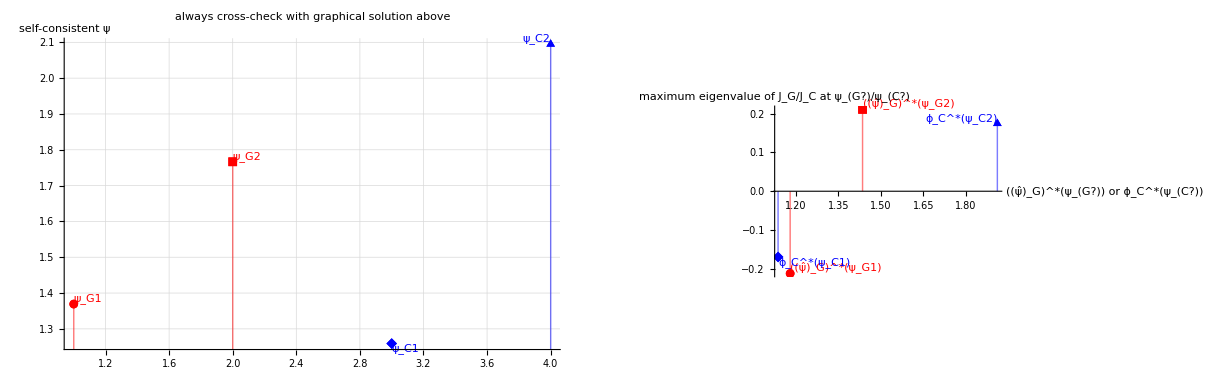

```mathematica
(*searching self-consistent ψ and computing stability of ensemble dynamics for variable coupling strength λ and fixed g and weights*)
λ=0.16;
(*search routines for self-consistent Subscript[ψ, G]. For random regular graphs, there are (usually) at most 2 self-consistent ψ per ensemble dynamics. Use above graphical solution for rough idea about number of solutions and their approximate values. Introduce Subscript[ψ, G3], ... and Subscript[ψ, C3], ... if needed :*)
Subscript[ψ, G1]=findψG[λ,1];(*find first value for generator dynamics, place initial value of search close to intersection in graph*)
Subscript[ψ, G2]=findψG[λ,1.7];(*find second value for generator dynamics, place initial value of search close to intersection in graph*)
Subscript[ψ, C1]=findψC[λ,1.2];(*find first value for consumer dynamics, place initial value of search close to intersection in graph*)
Subscript[ψ, C2]=findψC[λ,2.1];(*find second value for consumer dynamics, place initial value of search close to intersection in graph*)

(*------  internal functions for linear stability analysis, go to end of block for graphical output  ---------*)
consistentψ={{1,Subscript[ψ, G1]},{2,Subscript[ψ, G2]},{3,Subscript[ψ, C1]},{4,Subscript[ψ, C2]}};(*array*)
(*compute maximum real part of generator Jacobian's spectrum at given self-consisten ψ; if negative, then fixed point linearly stable; unstable if positive*)
Subscript[maxEVψ, G1]=Max[Re[Eigenvalues[Jg/.cosψ-> Cos[Subscript[ψ, G1]]/.sinψ->Sin[Subscript[ψ, G1]]]]];
Subscript[maxEVψ, G2]=Max[Re[Eigenvalues[Jg/.cosψ-> Cos[Subscript[ψ, G2]]/.sinψ->Sin[Subscript[ψ, G2]]]]];
Subscript[maxEVψ, C1]=Max[Re[Eigenvalues[Jc/.cosψ-> Cos[Subscript[ψ, C1]]/.sinψ->Sin[Subscript[ψ, C1]]]]];
Subscript[maxEVψ, C2]=Max[Re[Eigenvalues[Jc/.cosψ-> Cos[Subscript[ψ, C2]]/.sinψ->Sin[Subscript[ψ, C2]]]]];
spectrumMax={{ψG[g,λ,Sin[Subscript[ψ, G1]],Cos[Subscript[ψ, G1]]],Subscript[maxEVψ, G1]},{ψG[g,λ,Sin[Subscript[ψ, G2]],Cos[Subscript[ψ, G2]]],Subscript[maxEVψ, G2]},{φC[g,λ,Sin[Subscript[ψ, C1]],Cos[Subscript[ψ, C1]]],Subscript[maxEVψ, C1]},{φC[g,λ,Sin[Subscript[ψ, C2]],Cos[Subscript[ψ, C2]]],Subscript[maxEVψ, C2]}};
colorList={Red, Red,Blue, Blue};
consistentψColor={#}&/@ consistentψ;
spectrumMaxColor={#}&/@ spectrumMax;
plot1=ListPlot[consistentψColor, PlotLabel->"always cross-check with graphical solution above", PlotStyle->colorList, PlotRange->All, Ticks->{{},Automatic}, Filling->Axis,  PlotMarkers->Automatic,AxesLabel->{"","self-consistent ψ"}, ImageSize->Scaled[1.3],  GridLines->Automatic, Epilog->{{Red,Text["ψ_G1",{1,Subscript[ψ, G1]},{-1,-1}]},{Red,Text["ψ_G2",{2,Subscript[ψ, G2]},{-1,-2}]},{Blue,Text["ψ_C1",{3,Subscript[ψ, C1]},{-1,2}]},{Blue,Text["ψ_C2",{4,Subscript[ψ, C2]},{1,-1}]}}];plot2=ListPlot[spectrumMaxColor,PlotStyle->colorList, PlotRange->All,  Filling->Axis,PlotMarkers->Automatic, AxesLabel->{"((ψ̂)_G)^*(ψ_(G?)) or ϕ_C^*(ψ_(C?))", "maximum eigenvalue of J_G/J_C at ψ_(G?)/ψ_(C?) "} ,ImageSize->Scaled[1.3],Epilog->{{Red,Text["((ψ̂)_G)^*(ψ_G1)",{ψG[g,λ,Sin[Subscript[ψ, G1]],Cos[Subscript[ψ, G1]]],Subscript[maxEVψ, G1]},{-1,-1}]},{Red,Text["((ψ̂)_G)^*(ψ_G2)",{ψG[g,λ,Sin[Subscript[ψ, G2]],Cos[Subscript[ψ, G2]]],Subscript[maxEVψ, G2]},{-1,-2}]},{Blue,Text["ϕ_C^*(ψ_C1)",{φC[g,λ,Sin[Subscript[ψ, C1]],Cos[Subscript[ψ, C1]]],Subscript[maxEVψ, C1]},{-1,2}]},{Blue,Text["ϕ_C^*(ψ_C2)",{φC[g,λ,Sin[Subscript[ψ, C2]],Cos[Subscript[ψ, C2]]],Subscript[maxEVψ, C2]},{1,-1}]}}(*"maxEV[((ψ̂)_G)^*(ψ_G1)]",{"maxEV([((ψ̂)_G)^*(ψ_G2)]",2},{"maxEV[ϕ_C^*(ψ_C1)]",3},{"maxEV[ϕ_C^*(ψ_C2)]",4}*)];
GraphicsRow[{plot1,plot2}]
```